# Пример численного интегрирования уравнений движения твёрдого тела

Юдинцев В. В. Самарский университет

#### Обобщенные координаты

```mathematica
qa={ψ[t],θ[t],φ[t]};dqa=D[qa,t];
qc={x[t],y[t],z[t]};dqc=D[qc,t];
w={w1[t],w2[t],w3[t]};
```

#### Матрица угловой скорости (кососимметрическая)

```mathematica
Tilde[w_]:={{0,-w[[3]],w[[2]]},{w[[3]],0,-w[[1]]},{-w[[2]],w[[1]],0}};
```

#### Построение матрицы поворота по углам Брайнта (x-y’-z’’)

```mathematica
E2A[ψ_,θ_,φ_]=({{1,0,0},{0,Cos[ψ],-Sin[ψ]},{0,Sin[ψ],Cos[ψ]}}).({{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}}).({{Cos[φ],-Sin[φ],0},{Sin[φ],Cos[φ],0},{0,0,1}});
```

#### Кинематические уравнения по углам Брайнта

```mathematica
(* Из кинематических уравнений для элементов матрицы поворота, выраженной через углы Брайнта *)
Solve[MapThread[Equal,{Flatten[D[E2A@@qa,t]],Flatten[(E2A@@qa).Tilde[w]]}],dqa]//FullSimplify
(* определяем производные углов Брайнта *)
kinematicEquation=Flatten[%/.Rule->Equal]
```

{{ψ'[t]→Sec[θ[t]] (Cos[φ[t]] w1[t]-Sin[φ[t]] w2[t]),θ'[t]→Sin[φ[t]] w1[t]+Cos[φ[t]] w2[t],φ'[t]→Tan[θ[t]] (-Cos[φ[t]] w1[t]+Sin[φ[t]] w2[t])+w3[t]}}

{ψ'[t]==Sec[θ[t]] (Cos[φ[t]] w1[t]-Sin[φ[t]] w2[t]),θ'[t]==Sin[φ[t]] w1[t]+Cos[φ[t]] w2[t],φ'[t]==Tan[θ[t]] (-Cos[φ[t]] w1[t]+Sin[φ[t]] w2[t])+w3[t]}

#### Сила и момент, действующие на твердое тело

Пусть сила приложена вдоль продольной оси осесимметричного тела и смещена от продольной оси  на расстояние √2δ

```mathematica
Fth={Fx,0,0}; ρth={0,δ,δ};
Mth=Cross[ρth,Fth];
```

#### Динамические уравнения Эйлера + кинематические уравнения

```mathematica
eqC=MapThread[Equal,{m D[dqc,t],(E2A@@qa).Fth}];
eqA={
J1 w1'[t]==(J2-J3) w2[t]*w3[t]+Mth[[1]],
J2 w2'[t]==(J3-J1) w1[t]*w3[t]+Mth[[2]],
J3 w3'[t]==(J1-J2) w2[t]*w1[t]+Mth[[3]]
};
eqA=MapThread[Equal,{DiagonalMatrix[{J1,J2,J3}].D[w,t],-Cross[w,DiagonalMatrix[{J1,J2,J3}].w]+Mth}]//FullSimplify;
eq=Flatten[{eqC,eqA,kinematicEquation}]
```

{m x''[t]==Fx Cos[θ[t]] Cos[φ[t]],m y''[t]==Fx (Cos[ψ[t]] Sin[φ[t]]+Cos[φ[t]] Sin[θ[t]] Sin[ψ[t]]),m z''[t]==Fx (-Cos[φ[t]] Cos[ψ[t]] Sin[θ[t]]+Sin[φ[t]] Sin[ψ[t]]),(J2-J3) w2[t] w3[t]==J1 w1'[t],Fx δ+(-J1+J3) w1[t] w3[t]==J2 w2'[t],Fx δ+J3 w3'[t]==(J1-J2) w1[t] w2[t],ψ'[t]==Sec[θ[t]] (Cos[φ[t]] w1[t]-Sin[φ[t]] w2[t]),θ'[t]==Sin[φ[t]] w1[t]+Cos[φ[t]] w2[t],φ'[t]==Tan[θ[t]] (-Cos[φ[t]] w1[t]+Sin[φ[t]] w2[t])+w3[t]}

#### Моменты инерции тела и начальные условия выбраны так, чтобы тело вращалось вокруг оси со средним значением момента инерции - J2 Также добавлено незначительное возмущение угловой скорсоти ω_1, ω_3 ≈ 0.001 рад/с.

```mathematica
params={m->50,Fx->1000,δ->0.005,J1->5,J2->20,J3->20,ψ0->0.0,θ0->0.0,φ0->0.0,w10->5,w20->0,w30->0};
```

#### Формируем уравнения и начальные условия для численного интегрирования

```mathematica
initials=MapThread[Equal,{#[[1]],#[[2]]}]&/@{{qc,{0,0,0}},{dqc,{0,0,0}},{w,{w10,w20,w30}},{qa,{ψ0,θ0,φ0}}}/.t->0;
neq={eq,initials}//.params//Flatten
```

{50 x''[t]==1000 Cos[θ[t]] Cos[φ[t]],50 y''[t]==1000 (Cos[ψ[t]] Sin[φ[t]]+Cos[φ[t]] Sin[θ[t]] Sin[ψ[t]]),50 z''[t]==1000 (-Cos[φ[t]] Cos[ψ[t]] Sin[θ[t]]+Sin[φ[t]] Sin[ψ[t]]),0==5 w1'[t],5.+15 w1[t] w3[t]==20 w2'[t],5.+20 w3'[t]==-15 w1[t] w2[t],ψ'[t]==Sec[θ[t]] (Cos[φ[t]] w1[t]-Sin[φ[t]] w2[t]),θ'[t]==Sin[φ[t]] w1[t]+Cos[φ[t]] w2[t],φ'[t]==Tan[θ[t]] (-Cos[φ[t]] w1[t]+Sin[φ[t]] w2[t])+w3[t],x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==0,w1[0]==5,w2[0]==0,w3[0]==0,ψ[0]==0.,θ[0]==0.,φ[0]==0.}

#### Выполняем интегрирование и строим графики угловых скоростей тела

```mathematica
tk=5;
sol=NDSolve[neq,Flatten[{w,qa,qc,dqc}],{t,0,tk}]//Flatten;
```

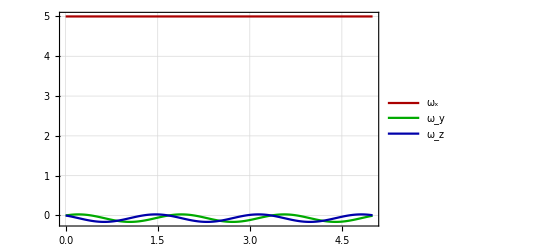

```mathematica
Plot[{w1[t],w2[t],w3[t]}//.%//Evaluate,{t,0,tk},PlotStyle->Darker[{Red,Green,Blue}],PlotTheme->"Detailed",PlotLegends->Placed[{"ω_x","ω_y","ω_z"},Above]]
```

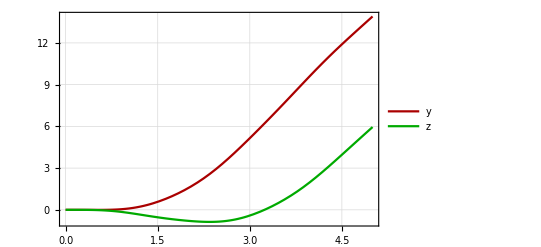

```mathematica
Plot[{y[t],z[t]}//.sol//Evaluate,{t,0,tk},PlotStyle->Darker[{Red,Green,Blue}],PlotTheme->"Detailed",PlotLegends->Placed[{"y","z"},Above]]
```

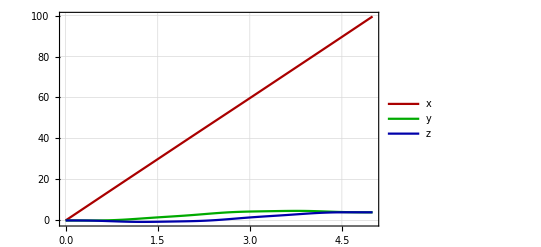

```mathematica
Plot[{x'[t],y'[t],z'[t]}//.sol//Evaluate,{t,0,tk},PlotStyle->Darker[{Red,Green,Blue}],PlotTheme->"Detailed",PlotLegends->Placed[{"x","y","z"},Above]]
```

```mathematica
x_□^□,2
```